# Valores de corte utilizando estadística de Anderson-Darling

## Definiciones

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{NotebookDirectory[],"AdvancedMapping.wl"}]];
```

```mathematica
Returns[prices_, lag_:1]:= N[Log[Drop[prices,lag]]-Log[Drop[prices,-lag]]];
```

```mathematica
AndersonDarling[data_,γ_]:= Block[{s, n,α,z,A2},
s = Sort[data];
n = Count[s,x_/;x≥γ];
If[n>1,
s = s[[-n;;-1]];
α = (1/n Sum[Log[s[[i]]/γ],{i,1,n}])^-1;
z = Table[1-(γ/s[[i]])^α,{i,1,n}];
A2 = -n-1/n Sum[(2i-1)(Log[z[[i]]]+Log[1-z[[n-i+1]]]),{i,1,n}]; 
Return[A2];,
Return[∞];
];
];
LeftADPlot[data_,γmin_,γmax_,dγ_]:=Block[{},
Print[
DiscretePlot[AndersonDarling[data,γ],{γ,γmin,γmax,dγ},PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"γ","A^2"},BaseStyle->FontSize->14,ImageSize->400]
];
];
RightADPlot[data_,γmin_,γmax_,dγ_]:=Block[{left},
left = LeftCutoff[data,γmin,γmax,dγ];
Print[
DiscretePlot[AndersonDarling[data,γ],{γ,left,γmax,dγ},PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"δ","A^2"},BaseStyle->FontSize->14,ImageSize->400]
];
];
LeftCutoff[data_,γmin_,γmax_,dγ_]:=Block[{tbl,minPos},
tbl = ProgressParallelTable[{γ,AndersonDarling[data,γ]},{γ,γmin,γmax,dγ},"Label"->"Finding left cutoff...",Method->"CoarsestGrained"];
tbl = DeleteCases[tbl,{_,∞}];
minPos =Position[tbl[[All,2]],Min[tbl[[All,2]]]][[1,1]];
Return[tbl[[minPos,1]]];
];

RightCutoff[data_,γmin_,γmax_,dγ_]:=Block[{tbl,maxPos,left},
left = LeftCutoff[data,γmin,γmax,dγ];
tbl = ProgressParallelTable[{γ,AndersonDarling[data,γ]},{γ,γmax,left,-dγ},"Label"->"Finding right cutoff...",Method->"CoarsestGrained"];
tbl = DeleteCases[tbl,{_,∞}];
maxPos =Position[tbl[[All,2]],Max[tbl[[All,2]]]][[1,1]];
Return[tbl[[maxPos,1]]];
];
ExtremeValuesPlot[data_,γmin_,γmax_,dγ_]:=Block[{l,pts,model,leftcutoff,pltmin,pltmax,k,α, datatofit},
pltmin = Min[data];
pltmax = Max[data];
leftcutoff = LeftCutoff[data,γmin,γmax,dγ];
l = HistogramList[data,Automatic,"PDF"];
pts = Transpose[{l[[1]][[2;;-1]],l[[2]]}];

Print[
Show[
ListLogLogPlot[pts,PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"x", "PDF"},GridLines->{{leftcutoff},{}},BaseStyle->FontSize->14,ImageSize->400]
]
];
];
```

## Ejemplo 1: Retornos S&P 500

```mathematica
ImportFinancialData[path_]:=Block[{data, years, month, day, price, date},
data = Import[path];
years = data[[All,1]];
month = data[[All,2]];
day = data[[All,3]];
price = data[[All,4]];
date = Transpose[{years,month,day}];
Return[Transpose[{Drop[date,1],Returns[price]}]];
];
```

Importa los datos y genera la sección positiva y negativa.

```mathematica
data = ImportFinancialData[NotebookDirectory[]<>"sAndP.csv"][[All,2]];
posData = Select[data,#>0&];
negData = -Select[data,#<0&];
```

Muestra los valores de γ de los puntos de corte derecho e izquierdo.

```mathematica
LeftCutoff[posData, 0.01,0.06,0.0001]
```

0.0394

```mathematica
RightCutoff[posData, 0.02,Max[posData],0.00001]
```

0.102452

Gráfica logarítmica de los valores extremos con sus respectivos valores de corte.

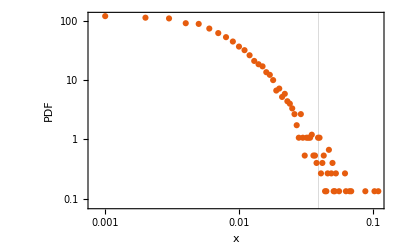

```mathematica
ExtremeValuesPlot[posData, 0.001,Max[posData],0.00001]
```

Gráfica de la estadística de Anderson-Darling para diferentes valores de γ

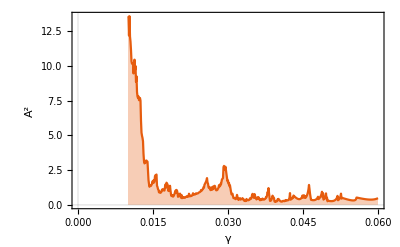

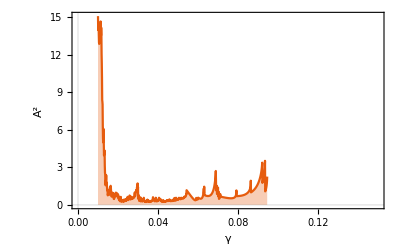

```mathematica
LeftADPlot[posData,0.01,0.06,0.0001]
LeftADPlot[negData,0.01,0.15,0.0001]
```

## Ejemplo 2: Riqueza de celdas en el juego de la vida

```mathematica
data = First@Transpose@Import[NotebookDirectory[]<>"gol0.2a.dat"];
```

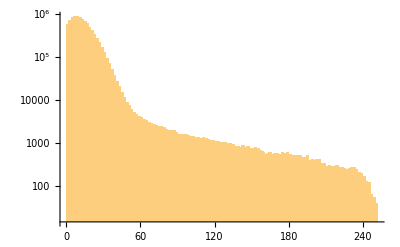

```mathematica
Histogram[data,ScalingFunctions->"Log",PlotRange->All]
```

```mathematica
LeftCutoff[data, 20.5,100,1]-0.5
```

44.

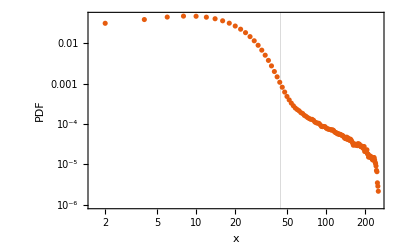

```mathematica
ExtremeValuesPlot[data, 20.5,100,1]
```